```mathematica
Charting`$InteractiveHighlighting=False
```

False

## Calibration line

```mathematica
titles={"Background","Ag","Fe","Ge","Mn","Ni","Unknown sample"};
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/XDET/xrdData/``.txt",#],"Table","HeaderLines"->6,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"Channel"->1,"Counts per second (Hz)"->2|>]&/@{"Backg","Ag","Fe","Ge","Mn","Ni","Sample"};
```

```mathematica
data2=Transpose[{#[All,"Channel"],#[All,"Counts per second (Hz)"]}//Normal]&/@data;
```

```mathematica
cPeaks=FindPeaks[#,Automatic,Automatic,12]&/@(TimeSeriesResample@TimeSeries[#2,{#1}]&@@@(Transpose[Take[#,573]]&/@data2))//Normal;
```

```mathematica
Rule@@@Transpose[{titles,Column@Flatten@Take[#,All,1]&/@cPeaks}]//Association//Dataset
```

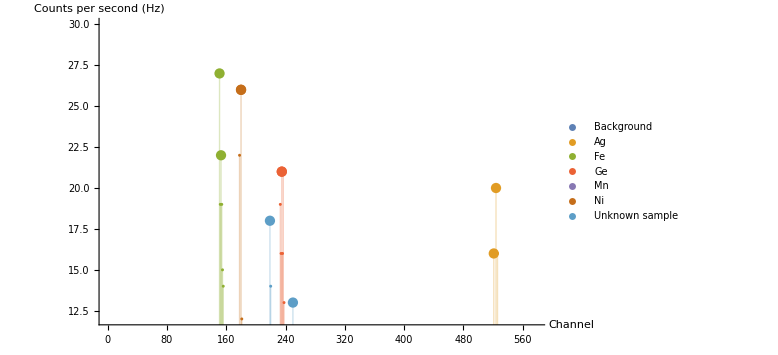

```mathematica
ListPlot[Take[#,573]&/@data2,PlotRange->All,AxesLabel->{"Channel","Counts per second (Hz)"},Filling->Axis]//Show[#,ListPlot[cPeaks/. {}->{0,0}//Evaluate,PlotLegends->Placed[titles,Below]],ImageSize->Large,PlotRange->{Full,{12,30}}]&
```

```mathematica
manData=Transpose[{{524,151,235,180},{22.163,6.4,9.88,7.48}}]; (* Manually filtered data from the results *)
```

```mathematica
fitfn=LinearModelFit[manData,x,x]
```

FittedModel[-0.0849263+0.0424428 x]

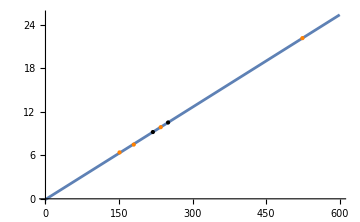

```mathematica
Plot[fitfn[x],{x,0,600},Epilog->{PointSize[Large],Orange,Point[manData],Black,Point[{#,fitfn[#]}&/@{219,250}]},ImageSize->Medium]
```

```mathematica
fitfn[#]&/@{219,250} (* It seems like GaAs *)
```

{9.21006,10.5258}

```mathematica
Entity["Chemical","GalliumArsenide"]
```

gallium arsenide

```mathematica
a=fitfn["BestFitParameters"][[2]]
```

0.0424428